# Combined Analysis Ω_DM and Direct Detection limits from lux

List of model parameters

#### Relative Abundance

#### Ω=0.1198+-0.0026

```mathematica
Ωexp = 0.1198; Ωerr = 0.0026; 
vev = 246; 
time1 = SessionTime[];
```

```mathematica
v=246.;
Mpl=1.22093 10^(19);
mw=80.385;
mz=91.1876;
MH=125.0;
GH=.01;
mτ=1.77682;
ΓZ=2.495;
mτ=1.77682;
MTA=mτ;
mh=125.7;
mb=4.66;
MZ=mz;
MB=mb;
cw=mw/mz;
sw=Sqrt[1-cw^2];
gew=2*mw/v;
Gz=2.495;
θ[s_]:=(1+Sign[s])/2;
w=ArcCos[80.385/91.1876];
mt=173.21;
mf=mt;
```

```mathematica
gs[T_]:=2+8*2+3*2*θ[T-mw]+3 θ[T-mz]+θ[T-mh]+(7/8) (2*(4+2+12+12)+4 θ[T-mτ]+2+12 θ[T-mb]+12 θ[T-mt]);
g=1;(*scalar particle*)(*relic abundance*)(* <σ v>:*)
```

```mathematica
sigmav[lsk_,mdm_]:=(3 lsk^2 MB^2 (-MB^2+mdm^2))/ (8 (-4 mdm^3+mdm MH^2)^2 Pi)
xf[mdm_,lsk_]:=Log[0.038 (g/Sqrt[gs[mdm]]) Mpl mdm sigmav[mdm,lsk]]-(1/2) Log[Log[0.038 (g/Sqrt[gs[mdm]]) Mpl mdm sigmav[mdm,lsk]]];
Ω[mdm_,lsk_]:=1.07 10^9 xf[mdm,lsk]/(Sqrt[gs[mdm]] Mpl sigmav[mdm,lsk]);
```

```mathematica
Ω[.005,63]
```

```mathematica
0.11364079650756156
```

```mathematica
Micromegas = .307
```

```mathematica
sigmav[.001,63]
```

4.09188×10^-11

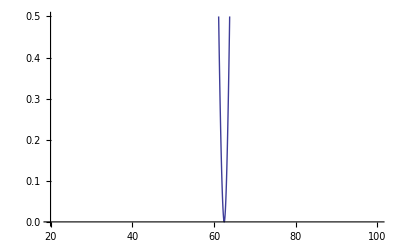

```mathematica
Plot[Ω[.006,mdm],{mdm,20,100},PlotRange->{0,.5}]
```